```mathematica
Polynomial cutoffs with smoothness.
```

-1/r^2

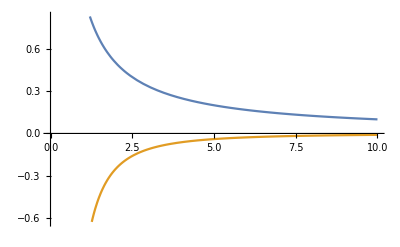

```mathematica
Dr=D[1/r,r]
Plot[{1/r,Dr},{r,0.001,10}]
```

Two cutoffs SR and LR. at both we want continuity and

```mathematica
D[1/r,r]
D[1/r,{r,2}]
```

-1/r^2

2/r^3

```mathematica
(D[Kernel[r],{r,2}]/.r->SRInner)==0.0,
(D[Kernel[r],{r,2}]/.r->LROuter)==0.0,

(D[Kernel[r],{r,2}]/.r->SROuter)==2/SROuter^3,
(D[Kernel[r],{r,2}]/.r->LRInner)==2/LRInner^3,
```

```mathematica
SRInner = 4.5;
SROuter =7.0;
LRInner=13.;
LROuter=15.;
Kernel[r_]:=(a+b*r^1+c*r^2+d*r^3+e*r^4+f*r^5+g*r^6+h*r^7)/r;
eqns={
(Kernel[SROuter]==1/SROuter)
,(Kernel[LRInner]==1/LRInner),
(D[Kernel[r],r]/.r->SROuter)==(-1/SROuter^2),
(D[Kernel[r],r]/.r->LRInner)==(-1/LRInner^2),

(D[Kernel[r],{r,2}]/.r->SROuter)==2/SROuter^3,
(D[Kernel[r],{r,2}]/.r->LRInner)==2/LRInner^3,
(D[Kernel[r],r]/.r->SRInner)==0.0,
(D[Kernel[r],r]/.r->LROuter)==0.0}
```

{0.142857 (a+7. b+49. c+343. d+2401. e+16807. f+117649. g+823543. h)==0.142857,0.0769231 (a+13. b+169. c+2197. d+28561. e+371293. f+4.82681×10^6 g+6.27485×10^7 h)==0.0769231,0.142857 (b+14. c+147. d+1372. e+12005. f+100842. g+823543. h)-0.0204082 (a+7. b+49. c+343. d+2401. e+16807. f+117649. g+823543. h)==-0.0204082,0.0769231 (b+26. c+507. d+8788. e+142805. f+2.22776×10^6 g+3.37877×10^7 h)-0.00591716 (a+13. b+169. c+2197. d+28561. e+371293. f+4.82681×10^6 g+6.27485×10^7 h)==-0.00591716,0.142857 (2 c+42. d+588. e+6860. f+72030. g+705894. h)-0.0408163 (b+14. c+147. d+1372. e+12005. f+100842. g+823543. h)+0.0058309 (a+7. b+49. c+343. d+2401. e+16807. f+117649. g+823543. h)==0.0058309,0.0769231 (2 c+78. d+2028. e+43940. f+856830. g+1.55943×10^7 h)-0.0118343 (b+26. c+507. d+8788. e+142805. f+2.22776×10^6 g+3.37877×10^7 h)+0.000910332 (a+13. b+169. c+2197. d+28561. e+371293. f+4.82681×10^6 g+6.27485×10^7 h)==0.000910332,-0.0493827 (a+4.5 b+20.25 c+91.125 d+410.063 e+1845.28 f+8303.77 g+37366.9 h)+0.222222 (b+9. c+60.75 d+364.5 e+2050.31 f+11071.7 g+58126.4 h)==0.,0.0666667 (b+30. c+675. d+13500. e+253125. f+4.55625×10^6 g+7.97344×10^7 h)-0.00444444 (a+15. b+225. c+3375. d+50625. e+759375. f+1.13906×10^7 g+1.70859×10^8 h)==0.}

```mathematica
sol=Solve[eqns,{a,b,c,d,e,f,g,h}]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{117649., 16807., 2401., 343., 49., 7., 1., 0.142857, -0.142857}, {4.82681×10^6, 371293., 28561., 2197., 169., 13., 1., 0.0769231, -0.0769231}, « 5 », {4.55625×10^6, 253125., 13500., 675., 30., 1., 0., -0.00444444, 0.}} may contain significant numerical errors.

{{a→-14.4612,b→11.6244,c→-3.69317,d→0.642583,e→-0.0661298,f→0.00402661,g→-0.00013439,h→1.89788×10^-6}}

```mathematica
OptKern[r_]:=(Kernel[r]/.{sol[[1]]})[[1]];
DOK[r_]:=D[(Kernel[rr]/.{sol[[1]]})[[1]],rr]/.{rr->r};
D2OK[r_]:=D[(Kernel[rr]/.{sol[[1]]})[[1]],{rr,2}]/.{rr->r};
```

```mathematica
Cutoff1r[r_]:=If[r<SRInner,OptKern[SRInner],If[r>LROuter,OptKern[LROuter],OptKern[r]]]
DCutoff1r[r_]:=If[r<SRInner,0.0,If[r>LROuter,0.0,DOK[r]]]
D2Cutoff1r[r_]:=If[r<SRInner,0.0,If[r>LROuter,0.0,D2OK[r]]]
```

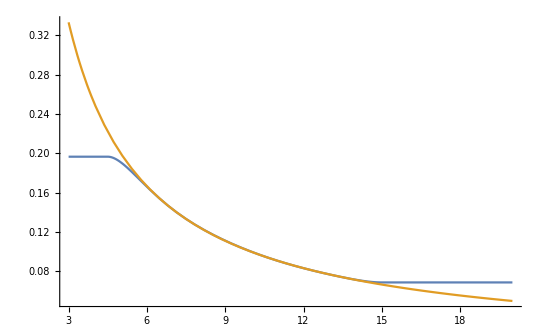

```mathematica
Plot[{Cutoff1r[r],1/r},{r,3,20.0}]
```

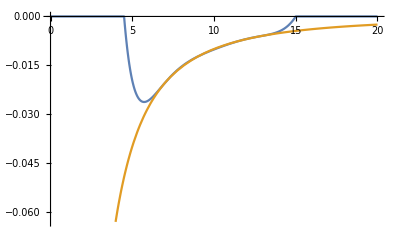

```mathematica
Plot[{DCutoff1r[r],-1/r^2},{r,0.001,20.0}]
```

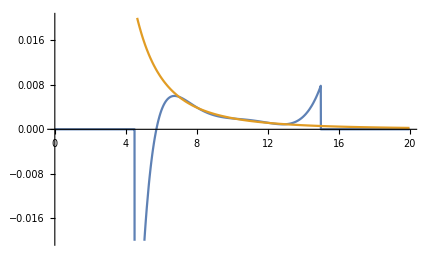

```mathematica
Plot[{D2Cutoff1r[r],2/r^3},{r,0.001,20.0},PlotRange->{All,{-0.02,0.02}}]
```

```mathematica
SRInner = 5.0;
SROuter =5.5;
LRInner=14.;
LROuter=15.;
Kernel[r_]:=a+b*r^1+c*r^2+d*r^3+e*r^4+f*r^5;
eqns={(D[Kernel[r]/r,r]/.r->SRInner)==0.0,
(D[Kernel[r]/r,r]/.r->LROuter)==0.0,
(Kernel[SROuter]==1.0)
,(Kernel[LRInner]==1.0)}
```

{b+10. c+75. d+500. e+3125. f==0.,b+30. c+675. d+13500. e+253125. f==0.,a+5.5 b+30.25 c+166.375 d+915.063 e+5032.84 f==1.,a+14. b+196. c+2744. d+38416. e+537824. f==1.}

```mathematica
SRInner = 5.0;
SROuter =5.5;
LRInner=14.;
LROuter=15.;
Kernel[r_]:=(a+b*r^1+c*r^2+d*r^3+e*r^4+f*r^5+g*r^6+h*r^7)/r;
eqns={
(Kernel[SROuter]==1/SROuter)
,(Kernel[LRInner]==1/LRInner),
(D[Kernel[r],r]/.r->SROuter)==(-1/SROuter^2),
(D[Kernel[r],r]/.r->LRInner)==(-1/LRInner^2),
(D[Kernel[r],{r,2}]/.r->SROuter)==2/SROuter^3,
(D[Kernel[r],{r,2}]/.r->LRInner)==2/LRInner^3,
(D[Kernel[r],r]/.r->SRInner)==0.0,
(D[Kernel[r],r]/.r->LROuter)==0.0}
```